```mathematica
ClearAll["Global`*"]
```

## Import Data

```mathematica
(* first column is data: 1900/1/1 is 1 *)
(*data0=Import[StringJoin[NotebookDirectory[],"2a - analysis - Count Love.xlsx"]]*)
data0=Import[StringJoin[NotebookDirectory[],"2b - analysis - MST 2013 - 2018.xlsx"]]
```

{{{43281.,Jersey City,5.,,,HudsonCounty,NewJersey,40.7114,-74.0648,1.},{43280.,Ashburn,8.,,,TurnerCounty,Georgia,31.7092,-83.6524,1.},{43279.,Annapolis,5.,,,AnneArundelCounty,Maryland,38.9723,-76.5064,1.},2131,{41275.,McKeesport,4.,,,AlleghenyCounty,Pennsylvania,40.3419,-79.845,1.},{41275.,Sacramento,5.,,,SacramentoCounty,California,38.5666,-121.469,1.}}}
 |  |  |  |

## Data Selection and Cleaning

```mathematica
(* select some data only; remove selection column *)
{{xMin,xMax},{yMin,yMax}}={{-130,-65},{25,50}}(*{{-170,-65},{25,70}}*);

data1=First@data0;

data1=Select[data1,#[[-1]]==1&];
data1=Drop[data1,None,{-1}]

data1=Select[data1,And[yMin<=#[[-2]]≤yMax,xMin<=#[[-1]]≤xMax]&];

(* remove cases with location N/A *)
data1=Select[data1,#[[-1]]≠"Failure"&];

(* filter out old dates *)
msAdj=1; (* Microsoft Excel mistaken let 1900/2/29 exist,which shouldn't *)
dateFilter=First@DateDifference[DateObject[{1900, 1, 1}],DateObject[{2017, 3, 3}]]+1+msAdj;
data1=Select[data1,#[[1]]>=dateFilter&];
firstdate=Min@data1[[All,1]];
firstdateD=DateObject[{1900, 1, 1}]+Quantity[firstdate-1-msAdj,"Days"]
```

{{43281.,Jersey City,5.,,,HudsonCounty,NewJersey,40.7114,-74.0648},{43280.,Ashburn,8.,,,TurnerCounty,Georgia,31.7092,-83.6524},{43279.,Annapolis,5.,,,AnneArundelCounty,Maryland,38.9723,-76.5064},1951,{41275.,McKeesport,4.,,,AlleghenyCounty,Pennsylvania,40.3419,-79.845},{41275.,Sacramento,5.,,,SacramentoCounty,California,38.5666,-121.469}}
 |  |  |  |

Day: Fri 3 Mar 2017

```mathematica
(* update 50k to 50,000 *)
times1000[s_]:=If[NumericQ[s],s,If[StringTake[s,-1]=="k",ToExpression[StringDrop[s,-1]]*1000,s]];
logtimes1000[s_]:=If[NumericQ[s],Log[s],If[StringTake[s,-1]=="k",Log[ToExpression[StringDrop[s,-1]]*1000],s]];
pplSize=times1000/@data1[[All,3]];
data1[[All,3]]=pplSize;
Take[data1,10]

(* Delete Duplicate *)
data1=SortBy[data1,{-#[[1]],-#[[3]]}&];
data1=DeleteDuplicatesBy[data1,#[[{1,-2,-1}]]&];
```

{{43281.,Jersey City,5.,,,HudsonCounty,NewJersey,40.7114,-74.0648},{43280.,Ashburn,8.,,,TurnerCounty,Georgia,31.7092,-83.6524},{43279.,Annapolis,5.,,,AnneArundelCounty,Maryland,38.9723,-76.5064},{43278.,San Antonio,4.,,,BexarCounty,Texas,29.4724,-98.5251},{43278.,Oakland,4.,,,AlamedaCounty,California,37.7699,-122.226},{43278.,Hartford,4.,,,HartfordCounty,Connecticut,41.766,-72.6833},{43276.,Chicago (West Pullman),4.,,,CookCounty,Illinois,41.8376,-87.6818},{43276.,Chicago (Bronzeville),6.,,,CookCounty,Illinois,41.8376,-87.6818},{43275.,Santa Rosa,4.,,,SonomaCounty,California,38.4468,-122.706},{43275.,Riviera Beach,4.,,,PalmBeachCounty,Florida,26.7826,-80.0722}}

## Clustering

```mathematica
(* rescaling *)
(* Do Clustering *)

nStart=1;
nEnd=Length[data1]; (* or smaller; all = 6077*)

scaleTime1=175; (* need to find some meaningful thing traveling 100 degree per year to justify *)

nCts=Automatic;

(* created data2 = rescaled(data1)  *)
data2=MapAt[(#-firstdate)/365*scaleTime1&,data1,{All,1}];

(*data2[[All,1]]=data2[[All,1]]*scaleTime1;*)
{t,cts}=Timing@FindClusters[data2[[nStart;;nEnd,{1,-2,-1}]]->data2[[nStart;;nEnd]],nCts,DistanceFunction->EuclideanDistance];
 t

(* {t,cts}=Timing@FindClusters[data2[[nStart;;nEnd,{1,-2,-1}]]->data2[[nStart;;nEnd]],DistanceFunction->EuclideanDistance,Method->"Agglomerate"] *)
(* {t,cts}=Timing@FindClusters[data2[[nStart;;nEnd,{1,-2,-1}]]->data2[[nStart;;nEnd]],nCts,CriterionFunction->"CalinskiHarabasz"] *)
(*data2[[All,1]]=data2[[All,1]]/scaleTime1;*)

n=Length[cts]
```

1.98438

3

## Plotting

```mathematica
(* create the image of Geo Map *)

yManualAdj=0;

g1=(GeoPosition[{yMin+yManualAdj,#}]&/@Range[xMin,xMax,5]);
g2=(GeoPosition[{yMax+yManualAdj,#}]&/@Range[xMax,xMin,-5]);
img=Lighter@GeoGraphics[Polygon@Join[g1,g2],GeoProjection->"CylindricalEqualArea",GeoRangePadding->None];
```

```mathematica
(* year adj*)

ctsSel=cts[[All,All,{-1,-2,1}]];
MaxTime=Max@cts[[All,All,1]];
plotRange1={{xMin,xMax},{yMin,yMax},{0,MaxTime}};
boxRatios1={1.2,0.7,2};
slices={0,0.721,0.78,0.8,0.857,1}*MaxTime; 
 slicesB={0,MaxTime}; 
colCts=ColorData[97]/@Range[n];
timetick1=Table[{n,DateString[firstdateD+Quantity[n/scaleTime1,"Years"],{"Month","/","Day","/","YearShort"}]},{n,slices}]; (* 100 unit = 1 year *)

plot1=Plot3D[Drop[slices,-1],{x,xMin,xMax},{y,yMin,yMax},PlotRange->plotRange1,Ticks->{Automatic,Automatic,timetick1},BoxRatios->boxRatios1,PlotStyle->Texture[img]];
plot1B=Plot3D[Drop[slicesB,-1],{x,xMin,xMax},{y,yMin,yMax},PlotRange->plotRange1,Ticks->{Automatic,Automatic,timetick1},BoxRatios->boxRatios1,PlotStyle->Texture[img]];
plot2=ListPointPlot3D[ctsSel,PlotRange->plotRange1,Ticks->{Automatic,Automatic,timetick1},BoxRatios->boxRatios1];
plot3=Table[{HighlightMesh[ConvexHullMesh[ctsSel[[i]]],Style[2,colCts[[i]],Opacity[0.5]]]},{i,n}];

Show[{plot1B,plot2},ViewPoint->{-0.4,-1.1,2.3}]
Show[{plot1,plot2}]
Show[{plot1B,plot2,plot3}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
plot4=Graphics3D[{Transpose[{colCts,Point/@ctsSel}],Opacity[0.25],Transpose[{colCts,BoundingRegion[#,"FastEllipsoid"]&/@ctsSel}]}];

Show[{plot1B,plot4}]
```

-Graphics3D-

## Graph

```mathematica
IGMeshGraph[mesh_]:=Graph[Range@MeshCellCount[mesh,0],MeshCells[mesh,1][[All,1]],EdgeWeight->PropertyValue[{mesh,1},MeshCellMeasure],VertexCoordinates->MeshCoordinates[mesh],PlotTheme->"Default"];
f[{p_,q_}]:=Sqrt[p^2+q^2];

plot5All=nAllJ=statEdgeVecAllJ=corrEdgeVecAllJ=lambdasAllJ=ctsSelAllJλ=scaleGrowthAllJ={};

(*** diffussion analysis ***)

 For[j=1,j≤n,j++, (* select cluster *)
(* For[j=5,j≤5,j++, (* select cluster *) *)

(* create tree of the cluster *)

ctsSelJ=ctsSel[[j]];

graph=IGMeshGraph@DelaunayMesh[ctsSelJ];
plot5=FindSpanningTree[graph,VertexCoordinates->GraphEmbedding@graph,EdgeShapeFunction->"Line",EdgeStyle->{Thick,Black},VertexSize->Tiny,VertexStyle->Black,PlotTheme->"Default"];
plot5All=Append[plot5All,plot5];

nJ=VertexCount[plot5];
nAllJ=Append[nAllJ,nJ];

vtxCood=PropertyValue[plot5,VertexCoordinates];

(*** Edges Analysis ***)

edges=EdgeList[plot5];

(* edgeVectors = {combining Δlat and Δlong, Δtime} *)
edgeVectors=Table[vtxDiff=vtxCood[[edges[[n,1]]]]-vtxCood[[edges[[n,2]]]];{f[vtxDiff[[1;;2]]],Abs@vtxDiff[[3]]},{n,1,Length@edges}];

(* jump statistic *)
statEdge=Table[#@edgeVectors[[All,i]]&/@{Mean,StandardDeviation,Quantile[#,{1/4,1/2,3/4}]&},{i,1,2}];
statEdgeVecAllJ=Append[statEdgeVecAllJ,statEdge];

(* deg-time correlation *)
corrEdge=Correlation@edgeVectors;
corrEdgeVecAllJ=Append[corrEdgeVecAllJ,corrEdge[[1,2]]];

(* Gamma Distribution Modeling *)
distml=Table[EstimatedDistribution[edgeVectors[[All,i]],ExponentialDistribution[λ]],{i,1,2}];
{λ1,λ2}=1/Mean/@distml;
lambdasAllJ=Append[lambdasAllJ,{λ1,λ2}];

ctsSelJλ=ArrayFlatten[{{ctsSelJ,ConstantArray[{λ1,λ2,λ1*λ2},nJ]}}];
ctsSelAllJλ=Append[ctsSelAllJλ,ctsSelJλ];

(*** Study expected growth of scale; weight = log(scale) ***)

vtxScale=cts[[j]][[All,3]];

ratioVectors1=Table[
vtx1=edges[[n,1]];
vtx2=edges[[n,2]];
If[Or[vtxScale[[vtx1]]=="---",vtxScale[[vtx2]]=="---",vtxCood[[vtx1,3]]==vtxCood[[vtx2,3]]],
"---",
(vtxScale[[vtx1]]/vtxScale[[vtx2]])^-Order[vtxCood[[vtx1,3]],vtxCood[[vtx2,3]]]
]
,{n,1,Length@edges}];

scaleGrowthKnown=Exp@N@Mean@Log@Select[ratioVectors1,#≠"---"&];
scaleGrowthAllJ=Append[scaleGrowthAllJ,scaleGrowthKnown];

]
```

```mathematica
Manipulate[Legended[Show[{plot1B,plot5All[[i]]}],
Column[{{"i",nAllJ[[i]]},{Column@{"ΔDeg Stat","Δt Stat"},statEdgeVecAllJ[[i]]},{"corr",corrEdgeVecAllJ[[i]]},{"λ1, λ2",lambdasAllJ[[i]]},{"Scale Growth",scaleGrowthAllJ[[i]]}}]
],{i,Range@n,ControlType->SetterBar}]

ctsSelAllJλ=Flatten[ctsSelAllJλ,1];
nAllJ//Column
statEdgeVecAllJ//Column
corrEdgeVecAllJ//Column
lambdasAllJ//Column
scaleGrowthAllJ//Column
```

158
145
206

{{3.20943,2.42281,{1.36255,2.9977,4.6231}},{2.43391,2.18808,{0.958904,1.91781,3.35616}}}
{{3.18556,2.26442,{1.37809,2.77166,4.61198}},{2.22412,1.96305,{0.958904,1.91781,2.87671}}}
{{2.92672,2.21878,{1.16546,2.64174,4.28998}},{2.25459,2.08687,{0.479452,1.91781,3.35616}}}

-0.059958
0.0015764
-0.112904

{0.311582,0.410862}
{0.313917,0.449615}
{0.34168,0.443539}

1.00529
1.01588
0.968096

## Prediction

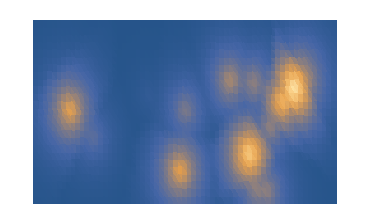

-Graphics-

```mathematica
(* Find nearest points towards the surface-tNow *) 

tNow=Ceiling@MaxTime+0;

precision=1;

tNowSurface=Flatten[Outer[{#1,#2,tNow}&,Range[xMin,xMax,precision],Range[yMin,yMax,precision]],1]; (* for step = 5 : size = 22*10 *)

nearestPtsIdx=Flatten[Nearest[ctsSelAllJλ[[All,1;;3]]->"Index"]/@tNowSurface,1];

nearestPtsCood=ctsSelAllJλ[[#,1;;3]]&/@nearestPtsIdx;
chosenλ=ctsSelAllJλ[[#,4;;5]]&/@nearestPtsIdx;
(* chosenλ=ConstantArray[Mean@chosenλ,Length@chosenλ]; (* used same λ1, λ2 for all points *) *)
chosenCoef=ctsSelAllJλ[[#,6]]&/@nearestPtsIdx;
(* chosenCoef=ConstantArray[Times@@Mean@chosenλ,Length@chosenCoef]; (* used same λ1*λ2 for all points *) *)

dist=MapThread[{f[#1[[1;;2]]-#2[[1;;2]]],Abs[#1[[3]]-#2[[3]]]}&,{tNowSurface,nearestPtsCood}];
pdfAdj=Exp@-MapThread[#1.#2&,{dist,chosenλ}];
pdfAdj=MapThread[#1*#2&,{pdfAdj,chosenCoef}];

valueSurface=ConstantArray[0,Dimensions@tNowSurface];
valueSurface[[All,1;;2]]=tNowSurface[[All,1;;2]];
valueSurface[[All,3]]=pdfAdj;

img2=ImageResize[img,{370,224}];
plot6=ListDensityPlot[valueSurface,AspectRatio->ImageAspectRatio@img2,PlotRangePadding->0,PlotRange->All,ImageSize->ImageDimensions[img2],Axes->False,Frame->None]
ImageAdd[ImageMultiply[plot6,0.5],ImageMultiply[img2,0.5]]
```